# Wechselspannung

```mathematica
Needs["ErrorBarLogPlots`"];
```

ω = 2ℼf

```mathematica
f = {137.0,733,35.46,4.080*10^(3),4.120*10^(3),480.0*10^(3),990*10^(3)}
```

{137.,733,35.46,4080.,4120.,480000.,990000}

```mathematica
sf = {0.5,1,0.03,5,500,1000,8000}
```

{0.5,1,0.03,5,500,1000,8000}

```mathematica
ue = {3.50,3.40,3.41,3.40,3.40,3.20,2.72}
```

{3.5,3.4,3.41,3.4,3.4,3.2,2.72}

```mathematica
sue = {0.1,0,0.01,0.01,0.01,0.01,0.02}
```

{0.1,0,0.01,0.01,0.01,0.01,0.02}

```mathematica
ua = {461*10^(-3),196*10^(-3),1.42,180*10^(-3),184*10^(-3),177*10^(-3),163*10^(-3)} //N
```

{0.461,0.196,1.42,0.18,0.184,0.177,0.163}

```mathematica
sua = {10^(-3),0,0.01,2*10^(-3),10^(-3),10^(-3),10^(-3)}
```

{1/1000,0,0.01,1/500,1/1000,1/1000,1/1000}

## Aufgabe 3

C = 100nF

R = 100kΩ

```mathematica
c = 100*10^(-9)
```

1/10000000

```mathematica
R=100*10^3
```

100000

```mathematica
a=Table[{f[[i]],Abs[ue[[i]]/ua[[i]]]/(2π*f[[i]]*c)}, {i, 1, Length[f]}]
```

{{137.,88199.6},{733,37665.1},{35.46,107782.},{4080.,7368.28},{4120.,7138.12},{480000.,59.9454},{990000,26.8266}}

```mathematica
b=Table[{f[[i]],Sqrt[1+(2π*f[[i]]*R*c)^2]/(2π*f[[i]]*c)}, {i, 1, Length[f]}]//N
```

{{137.,100673.},{733.,100024.},{35.46,109611.},{4080.,100001.},{4120.,100001.},{480000.,100000.},{990000.,100000.}}

```mathematica
a = Sort[a,#1[[1]]<#2[[1]]&]
```

{{35.46,107782.},{137.,88199.6},{733,37665.1},{4080.,7368.28},{4120.,7138.12},{480000.,59.9454},{990000,26.8266}}

```mathematica
b=Sort[b,#1[[1]]<#2[[1]]&]
```

{{35.46,109611.},{137.,100673.},{733.,100024.},{4080.,100001.},{4120.,100001.},{480000.,100000.},{990000.,100000.}}

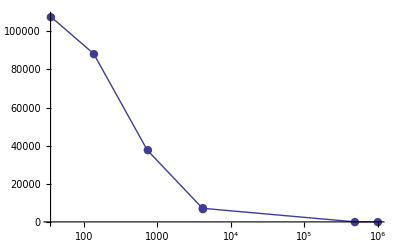

```mathematica
k = ListLogLinearPlot[a, Joined->True, PlotMarkers->{Automatic,Tiny}]
```

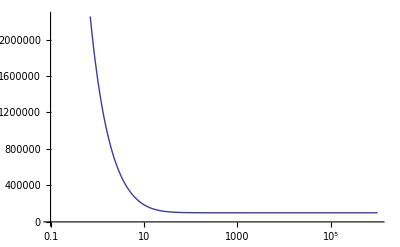

```mathematica
d = LogLinearPlot[Sqrt[1+(2π*ff*R*c)^2]/(2π*ff*c), {ff, 0.1, Max[f]}]
```

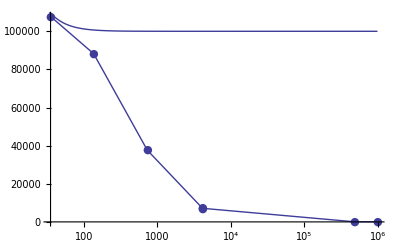

```mathematica
Show[k,d]
```

## Aufgabe 4

```mathematica
f = {58.7,23.50,607,296,3.425*10^(3),7.215*10^(3),36.64*10^(3),58.24*10^(3),177.8*10^(3),217.9*10^(3)};
```

```mathematica
sf = {0.07,0.03,2,0.2,50,1,0,10,300,500}
```

{0.07,0.03,2,0.2,50,1,0,10,300,500}

```mathematica
phi = {720*10^(-6),4.6*10^(-3),18*10^(-6),53.60*10^(-6),1.580*10^(-6),360*10^(-9),394*10^(-9),776*10^(-9),1.36*10^(-6),1.24*10^(-6)};
```

```mathematica
sphi = {50*10^(-6),0.1*10^(-3),0.5*10^(-6),1*10^(-6),0.1*10^(-6),30*10^(-9),15*10^(-9),6*10^(-9),0,0};
```

```mathematica
t = Table[{f[[i]], ArcTan[1/(2π*f[[i]]*R*c)]}, {i, 1, Length[f]}];
```

```mathematica
a = Table[{f[[i]], phi[[i]]*2π*f[[i]]}, {i, 1, Length[f]}];
```

```mathematica
a = Sort[a,#1[[1]]<#2[[1]]&];
```

```mathematica
t=Sort[t,#1[[1]]<#2[[1]]&] ;
```

```mathematica
a//N
```

{{23.5,0.679212},{58.7,0.265553},{296.,0.0996865},{607.,0.0686501},{3425.,0.0340015},{7215.,0.0163199},{36640.,0.0907051},{58240.,0.283964},{177800.,1.51932},{217900.,1.69769}}

```mathematica
LogLogPlot[ArcTan[1/x], {x,1,1000}];
```

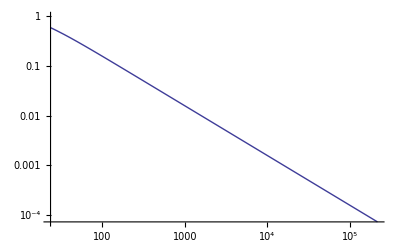

```mathematica
c = LogLogPlot[ArcTan[1/(2π*ff*R*c)], {ff, Min[f], Max[f]}]
```

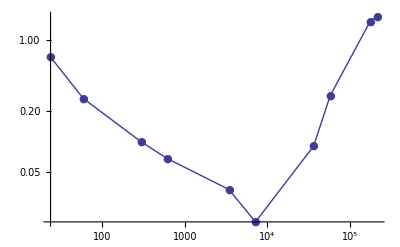

```mathematica
e = ListLogLogPlot[a, Joined->True, PlotMarkers->{Automatic,Tiny}]
```

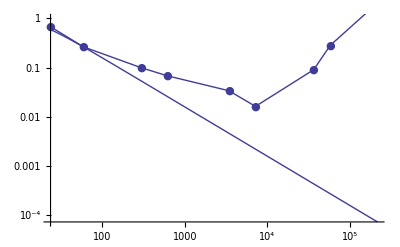

```mathematica
Show[c,e]
```